```mathematica
especies= 3;
metabolitos= 4;
```

```mathematica
n=especies;
m=metabolitos;
```

```mathematica
H = Table[RandomReal[{0.1,1}],m];
μ = Table[RandomReal[{0.01,0.1}],m];
δ = Table[RandomReal[{0.01,0.1}],n];
S = Table[RandomReal[5],m];
ciC = Table[RandomReal[5],m];
ciX = Table[RandomReal[5],n];
```

```mathematica
V = {
	{0,RandomReal[1],RandomReal[1]},
	{0,0,RandomReal[1]},
	{0,0,RandomReal[1]},
	{0,0,RandomReal[1]}
	};
W = {
	{RandomReal[1],0,0},
	{RandomReal[1],0,0},
	{0,RandomReal[1],0},
	{0,RandomReal[1],0}
};
```

```mathematica
V//MatrixForm;
```

```mathematica
W//MatrixForm;
```

```mathematica
concentrationsGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["c"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
speciesGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["x"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
G[c_, v_] := v.c
```

```mathematica
R[i_]:= (c[t]⟦i⟧)/(H⟦i⟧+c[t]⟦i⟧)
```

```mathematica
c[t_]=concentrationsGen[m];
x[t_] = speciesGen[n];
```

```mathematica
vars[t_]=Flatten[{c[t],x[t]}];
```

```mathematica
g =Table[ G[V⟦;;,i⟧,c[t]],{i,1,n}];
```

```mathematica
μμ= DiagonalMatrix[μ];
```

```mathematica
δδ=DiagonalMatrix[δ];
```

```mathematica
gg =DiagonalMatrix[g];
```

```mathematica
tt=(V-W).x[t]
```

{-0.485144 x1[t]+0.895878 x2[t]+0.689515 x3[t],-0.0118997 x1[t]+0.38326 x3[t],-0.131314 x2[t]+0.846379 x3[t],-0.411819 x2[t]+0.595818 x3[t]}

```mathematica
rr=Table[S⟦i⟧/tt⟦i⟧,{i,1,m}];
```

```mathematica
rrdiag=DiagonalMatrix[rr];
```

```mathematica
μc= μμ.c[t];
```

```mathematica
gδ=gg-δδ;
```

```mathematica
Wxr=(W.x[t]).rrdiag;
```

```mathematica
Vxr=(V.x[t]).rrdiag;
```

```mathematica
xgδ=x[t].gδ;
```

```mathematica
eqC = Table[c'[t]⟦i⟧==S⟦i⟧ +Wxr⟦i⟧-Vxr⟦i⟧-(μc⟦i⟧),{i,1,Length[c[t]]}]
eqX = Table[x'[t]⟦i⟧==xgδ⟦i⟧,{i,1,Length[x[t]]}];
cisC = Table[c[0]⟦i⟧==ciC⟦i⟧,{i,1,Length[c[t]]}];
cisX = Table[x[0]⟦i⟧==ciX⟦i⟧,{i,1,Length[x[t]]}];
```

{c1'[t]==4.33415-0.0333324 c1[t]+(2.10269 x1[t])/(-0.485144 x1[t]+0.895878 x2[t]+0.689515 x3[t])-(4.33415 (0.895878 x2[t]+0.689515 x3[t]))/(-0.485144 x1[t]+0.895878 x2[t]+0.689515 x3[t]),c2'[t]==4.68445-0.054825 c2[t]+(0.0557435 x1[t])/(-0.0118997 x1[t]+0.38326 x3[t])-(1.79537 x3[t])/(-0.0118997 x1[t]+0.38326 x3[t]),c3'[t]==2.57918-0.0674405 c3[t]+(0.338682 x2[t])/(-0.131314 x2[t]+0.846379 x3[t])-(2.18296 x3[t])/(-0.131314 x2[t]+0.846379 x3[t]),c4'[t]==3.46384-0.061579 c4[t]+(1.42648 x2[t])/(-0.411819 x2[t]+0.595818 x3[t])-(2.06382 x3[t])/(-0.411819 x2[t]+0.595818 x3[t])}

```mathematica
sistema = Flatten[{eqC,eqX,cisX,cisC}];
```

```mathematica
sol=NDSolve[sistema,vars[t],{t,0,10000}];
```

```mathematica
varc[t_]=Flatten[{c[t]}];
varx[t_] =Flatten[{x[t]}];
```

```mathematica
GraphC=NDSolve[sistema, varc[t],{t,0,100}];
```

```mathematica
GraphX= NDSolve[sistema, varx[t],{t,0,100}];
```

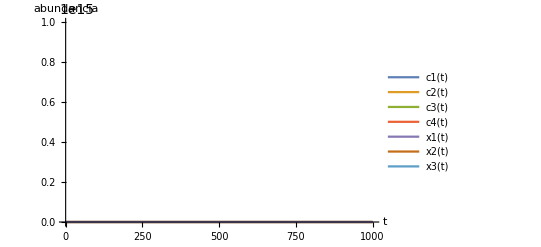

```mathematica
Plot[Evaluate[vars[t]/.sol],{t,0,1000},PlotLegends->vars[t],AxesLabel->{"t","abundancia"}]
```

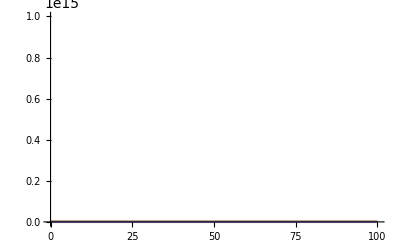

```mathematica
Plot[Evaluate[vars[t]/.sol],{t,0,100}]
```